```mathematica
Needs["CustomTicks`"]
```

```mathematica
FrameTicks->{LinTicks[0,5,1,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.008,MinorTickStyle->{Thick}],LinTicks[0,1,0.2,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.008,MinorTickStyle->{Thick}],None,None}
```

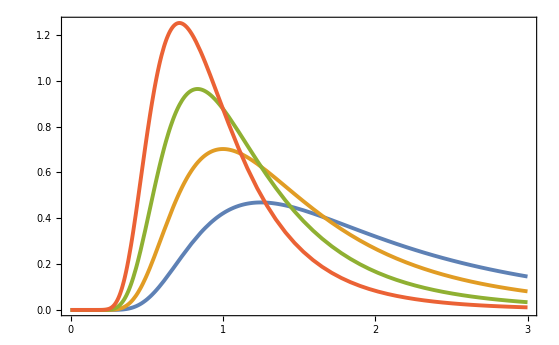

```mathematica
Plot[Evaluate@Table[PDF[InverseGammaDistribution[α,5],x],{α,{3,4,5,6}}],{x,0,3},PlotRange->All,PlotStyle->{Thickness[0.005]},Axes->False,Frame->True,FrameStyle->Directive[Thick,16,Bold],FrameTicks->{LinTicks[0,5,1,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],LinTicks[0,1.2,0.2,2,MajorTickLength->0.015,MajorTickStyle->{Thick},MinorTickLength->0.01,MinorTickStyle->{Thick}],None,None}]
```